```mathematica
J[x_,u_]:=6 x^2+u^2+4x u+3x+4u-9

Jplot = Plot3D[J[x,u],{x,-10,10},{u,-10,10},
AxesLabel->{"x","u","J"},
LabelStyle->{FontFamily->"Cambria Math",FontSize->14},
ColorFunction->"Rainbow",

PlotLegends->BarLegend[Automatic,
LabelStyle->{FontFamily->"Cambria Math",FontSize->14},LegendLabel->Style["J(x,u) = 6x^2+u^2+4xu+3x+4u-9",FontFamily->"Cambria Math",14]
]
]

SetDirectory["/home/eva/Documents/ITMO/4_course/tou/lab1/code"];
Export["../report/images/Jplot.pdf",Jplot,ImageResolution->600];
```

-Graphics3D-

```mathematica
J[x_,u_]:=6 x^2+u^2+4x u+3x+4u-9

surf = Plot3D[J[x,u],{x,-10,10},{u,-10,10},
AxesLabel->{"x","u","J"},
LabelStyle->{FontFamily->"Cambria Math",FontSize->14},
ColorFunction->"Rainbow",

PlotLegends->BarLegend[Automatic,
LabelStyle->{FontFamily->"Cambria Math",FontSize->14},LegendLabel->Style["J(x,u)",FontFamily->"Cambria Math",14]]
];

ptMin=ListPointPlot3D[
{{5/4,-(9/2),J[5/4,-(9/2)]}},
PlotStyle->{Black,PointSize[0.025]}
];

Jminplot=Show[surf,ptMin,
Epilog->{Inset[Framed[
Style["● (x^*, u^*)",FontFamily->"Cambria Math",14,Black],
Background->White,
FrameStyle->None,
RoundingRadius->2],
Scaled[{0.9,0.9}]
]
}
]


SetDirectory["/home/eva/Documents/ITMO/4_course/tou/lab1/code"];
Export["../report/images/Jminplot.pdf",Jminplot,ImageResolution->600];
```

-Graphics3D-

```mathematica
J[x_,u_]:=6 x^2+u^2+4x u+3x+4u-9
c[x_,u_] := 3x +4 u^2 +7
xConstr[u_]:=-(4 u^2+7)/3;

surf = Plot3D[J[x,u],{x,-10,10},{u,-10,10},
AxesLabel->{"x","u","J"},
LabelStyle->{FontFamily->"Cambria Math",FontSize->14},
ColorFunction->"Rainbow",

PlotLegends->BarLegend[Automatic,
LabelStyle->{FontFamily->"Cambria Math",FontSize->14},LegendLabel->Style["J(x,u)",FontFamily->"Cambria Math",14]]
];

line=ParametricPlot3D[{xConstr[u],u,J[xConstr[u],u]},{u,-2.5,2.5},
PlotStyle->{Red, Thickness[0.009]}
];

ptMin=Graphics3D[{Black,PointSize[0.03],Point[{-2.342,0.0788,J[-2.342,0.0788]}]}];

Jeqplot = Show[surf,line, ptMin,

Epilog->{Inset[Framed[
Style["● (x^*, u^*)",FontFamily->"Cambria Math",14,Black],
Background->White,
FrameStyle->None,
RoundingRadius->2],
Scaled[{0.9,0.9}]
]
}
]

SetDirectory["/home/eva/Documents/ITMO/4_course/tou/lab1/code"];
Export["../report/images/Jeqplot.pdf",Jeqplot,ImageResolution->600];
```

-Graphics3D-

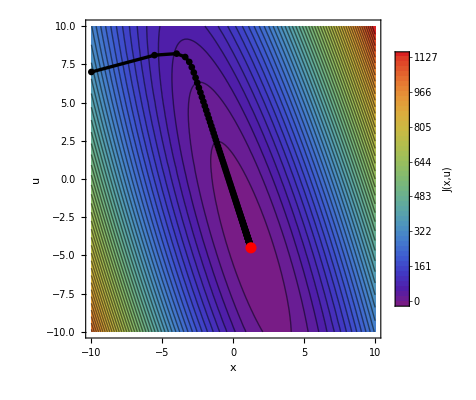

501

{1.25,-4.5}

```mathematica
J[x_,u_]:=6 x^2+u^2+4x u+3x+4u-9

hessJ = {{12, 4}, {4, 2}};
x0 = {-10, 7};
history = {x0};

gamma = 0.05;

gradNorm=Norm[Grad[J[x,u],{x,u}]/.{x->x0[[1]],u->x0[[2]]}];
tol=10^-6;

i=1;
While[i≤500 && gradNorm>tol,
gradNum=Grad[J[x,u],{x,u}]/.{x->x0[[1]],u->x0[[2]]};
xNew = x0  - gamma *gradNum;

x0 = xNew;
AppendTo[history,x0];

gradNorm=Norm[gradNum];
i++
]

jGamma005 = ContourPlot[J[x, u],{x,-10,10},{u,-10,10},

AxesLabel->{"x","u"},
LabelStyle->{FontFamily->"Cambria Math",FontSize->14},
ColorFunction->"Rainbow",

Epilog->{

Black,Thickness[0.006],Line[history],PointSize[0.012],Point[history],

Red,PointSize[0.02],Point[{1.25,-4.5}]
},


Contours->50,

PlotLegends->
BarLegend[Automatic,
LabelStyle->{FontFamily->"Cambria Math",FontSize->14},LegendLabel->Style["J(x,u)",FontFamily->"Cambria Math",14]]
]

Length[history]
history[[-1]]

SetDirectory["/home/eva/Documents/ITMO/4_course/tou/lab1/code"];
Export["../report/images/jGamma005.pdf",jGamma005,ImageResolution->600];
```

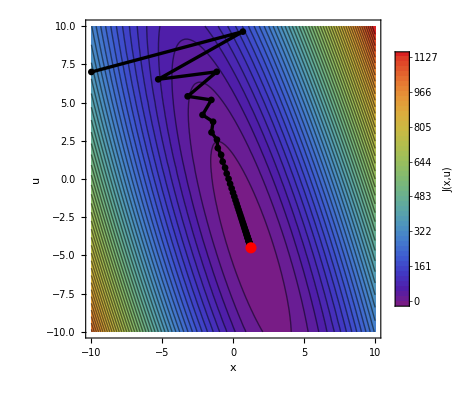

218

{1.25,-4.5}

```mathematica
J[x_,u_]:=6 x^2+u^2+4x u+3x+4u-9

hessJ = {{12, 4}, {4, 2}};
x0 = {-10, 7};
history = {x0};

gamma = 0.12;

gradNorm=Norm[Grad[J[x,u],{x,u}]/.{x->x0[[1]],u->x0[[2]]}];
tol=10^-6;

i=1;
While[i≤500 && gradNorm>tol,
gradNum=Grad[J[x,u],{x,u}]/.{x->x0[[1]],u->x0[[2]]};
xNew = x0  - gamma *gradNum;

x0 = xNew;
AppendTo[history,x0];

gradNorm=Norm[gradNum];
i++
]

jGamma012 = ContourPlot[J[x, u],{x,-10,10},{u,-10,10},

AxesLabel->{"x","u"},
LabelStyle->{FontFamily->"Cambria Math",FontSize->14},
ColorFunction->"Rainbow",

Epilog->{

Black,Thickness[0.006],Line[history],PointSize[0.012],Point[history],

Red,PointSize[0.02],Point[{1.25,-4.5}]
},


Contours->50,

PlotLegends->
BarLegend[Automatic,
LabelStyle->{FontFamily->"Cambria Math",FontSize->14},LegendLabel->Style["J(x,u)",FontFamily->"Cambria Math",14]
]
]

Length[history]
history[[-1]]

SetDirectory["/home/eva/Documents/ITMO/4_course/tou/lab1/code"];
Export["../report/images/jGamma012.pdf",jGamma012,ImageResolution->300];
```